The number of pixels and the FOV are limited by the laser repetition rate, i.e., how many laser pulses fit in a scanned line.
For a 80 MHz laser and 8 kHz scanner, there are 80 MHz/(2*8 kHz) = 5000 pulses. For example, if have 10 pulses per pixel, then there could be 500 pixels max

```mathematica
μm = 10^-6;
μs=10^-6;
ms=10^-3;
ns = 10^-9;
mm=10^-3;
kHz=10^3;
Tline=62.5μs;(*Time per scanned line*)
Tlaser = 12.5ns;(*Laser pulse repetition period*)
tFPGA = 6.25ns;(*Clock of the FPGA*)
Δx=0.5μm;(*Sampling resolution*)
γ=0.8;(*filling factor that removes the dead time at the turning points*)
FOV=γ L;(*Effective field of view of the microscope*)
NpixFull=500;(*Full pixel number*)
NpixPartial= γ NpixFull;(*Effective pixel number*)
L=NpixFull *Δx (*Full scan in μm*)
```

0.00025

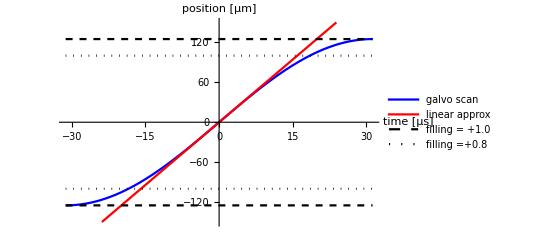

```mathematica
RSposition[t_]:=L/2 Sin[π/Tline t](*Position of the resonant scanner vs time*)
Plot[{RSposition[t μs]/μm,(L π)/(2Tline)t μs/μm,{L/2,-L/2}/μm,γ{L/2,-L/2}/μm },{t,-Tline/2/μs,Tline/2/μs},PlotRange->{-150,150},PlotStyle->{Blue,Red,{Dashed,Black},{Dotted,Black}},AxesLabel->{"time [μs]","position [μm]"} , PlotLegends->{"galvo scan","linear approx","filling = +1.0","filling =" +γ}]
```

```mathematica
DiscretePosition[pix_]:=Δx*pix(*Spatial discretization*)
```

```mathematica
time[x_]:=Tline/π ArcSin[2/L x](*Convert from spatial coordinate to time*)
DiscreteTime[pix_]:=Re[time[DiscretePosition[pix]]](*Time discretization mapped from the spatial discretization*)

AmplitudeFull= DiscretePosition[NpixFull/2];(*Amplitude of a full linescan. The FFOV is 2X this amount*)
tLinescanFull=2*DiscreteTime[NpixFull/2];(*Time to perform a full linescan (in half of the period, Tline/2)*)
AmplitudePartial= DiscretePosition[NpixPartial/2];(*Amplitude of a partial linescan. The FFOV is 2X this amount*)
tLinescanPartial=2*DiscreteTime[NpixPartial/2];(*Time to perform a partial linescan*)

(*Tabulate the position vs time*)
header={"pixel","Position [μm]","Time [μs]"};
TableForm[Prepend[Table[{pix,DiscretePosition[pix]/μm,DiscreteTime[pix]/μs},{pix,NpixFull/2,0,-1}],header]];
```

```mathematica
tdwell[pix_]:=DiscreteTime[pix]-DiscreteTime[pix-1](*Dwell time*)
PulsesPerPixel[pix_]:=tdwell[pix]/Tlaser (*Number of laser pulses that fit in the dwell time*)
PulsesPerPixelNorm[pix_]:=tdwell[0]/tdwell[pix](*Longer dwell times have a higher pulse counts. The pulse-count must be normalized*)

tLineScanFull = Sum[tdwell[i]/μs,{i,-NpixFull/2+1,NpixFull/2}];(*The sum of all the dwell times should equal a full scan. Compare*)
tLineScanPartial  = Sum[tdwell[i]/μs,{i,-NpixPartial/2+1,NpixPartial/2}];(*The sum of all the dwell times should equal the partial scan*)

(*Tabulate the dwell time*)
header={"pixel i","pixel i-1","Dwell [ns]","Pulses per pix", "Normalization factor"};
TableForm[Prepend[Table[{pix,pix-1,tdwell[pix]/ns,PulsesPerPixel[pix],PulsesPerPixelNorm[pix]},{pix,NpixPartial/2,1,-1}],header]]
```

pixel i | pixel i-1 | Dwell [ns] | Pulses per pix | Normalization factor
200. | 199. | 132.046 | 10.5637 | 0.602652
199. | 198. | 130.903 | 10.4723 | 0.607913
198. | 197. | 129.795 | 10.3836 | 0.613102
197. | 196. | 128.72 | 10.2976 | 0.618222
196. | 195. | 127.677 | 10.2142 | 0.623274
195. | 194. | 126.664 | 10.1331 | 0.62826
194. | 193. | 125.679 | 10.0543 | 0.633182
193. | 192. | 124.722 | 9.97777 | 0.63804
192. | 191. | 123.791 | 9.90331 | 0.642837
191. | 190. | 122.886 | 9.83088 | 0.647573
190. | 189. | 122.005 | 9.76037 | 0.652251
189. | 188. | 121.147 | 9.69173 | 0.656871
188. | 187. | 120.311 | 9.62486 | 0.661435
187. | 186. | 119.496 | 9.5597 | 0.665943
186. | 185. | 118.702 | 9.49619 | 0.670397
185. | 184. | 117.928 | 9.43425 | 0.674798
184. | 183. | 117.173 | 9.37384 | 0.679147
183. | 182. | 116.436 | 9.31489 | 0.683445
182. | 181. | 115.717 | 9.25736 | 0.687692
181. | 180. | 115.015 | 9.20118 | 0.691891
180. | 179. | 114.329 | 9.14632 | 0.696041
179. | 178. | 113.659 | 9.09273 | 0.700144
178. | 177. | 113.004 | 9.04035 | 0.7042
177. | 176. | 112.365 | 8.98916 | 0.70821
176. | 175. | 111.739 | 8.93911 | 0.712175
175. | 174. | 111.127 | 8.89017 | 0.716096
174. | 173. | 110.529 | 8.84229 | 0.719973
173. | 172. | 109.943 | 8.79545 | 0.723808
172. | 171. | 109.37 | 8.74961 | 0.7276
171. | 170. | 108.809 | 8.70473 | 0.731351
170. | 169. | 108.26 | 8.6608 | 0.735061
169. | 168. | 107.722 | 8.61778 | 0.73873
168. | 167. | 107.196 | 8.57564 | 0.74236
167. | 166. | 106.68 | 8.53436 | 0.745951
166. | 165. | 106.174 | 8.49392 | 0.749503
165. | 164. | 105.678 | 8.45428 | 0.753017
164. | 163. | 105.193 | 8.41542 | 0.756494
163. | 162. | 104.717 | 8.37733 | 0.759933
162. | 161. | 104.25 | 8.33998 | 0.763337
161. | 160. | 103.792 | 8.30335 | 0.766704
160. | 159. | 103.343 | 8.26743 | 0.770036
159. | 158. | 102.902 | 8.23218 | 0.773333
158. | 157. | 102.47 | 8.1976 | 0.776595
157. | 156. | 102.046 | 8.16367 | 0.779823
156. | 155. | 101.63 | 8.13037 | 0.783017
155. | 154. | 101.221 | 8.09768 | 0.786178
154. | 153. | 100.82 | 8.06559 | 0.789306
153. | 152. | 100.426 | 8.03408 | 0.792401
152. | 151. | 100.039 | 8.00314 | 0.795464
151. | 150. | 99.6595 | 7.97276 | 0.798496
150. | 149. | 99.2864 | 7.94291 | 0.801496
149. | 148. | 98.92 | 7.9136 | 0.804465
148. | 147. | 98.56 | 7.8848 | 0.807403
147. | 146. | 98.2063 | 7.85651 | 0.810311
146. | 145. | 97.8588 | 7.8287 | 0.813189
145. | 144. | 97.5173 | 7.80138 | 0.816037
144. | 143. | 97.1816 | 7.77453 | 0.818855
143. | 142. | 96.8517 | 7.74813 | 0.821645
142. | 141. | 96.5274 | 7.72219 | 0.824405
141. | 140. | 96.2085 | 7.69668 | 0.827138
140. | 139. | 95.8951 | 7.67161 | 0.829841
139. | 138. | 95.5869 | 7.64695 | 0.832517
138. | 137. | 95.2838 | 7.6227 | 0.835165
137. | 136. | 94.9857 | 7.59886 | 0.837786
136. | 135. | 94.6926 | 7.57541 | 0.840379
135. | 134. | 94.4043 | 7.55235 | 0.842945
134. | 133. | 94.1208 | 7.52966 | 0.845485
133. | 132. | 93.8418 | 7.50734 | 0.847998
132. | 131. | 93.5674 | 7.48539 | 0.850485
131. | 130. | 93.2974 | 7.46379 | 0.852946
130. | 129. | 93.0318 | 7.44255 | 0.855381
129. | 128. | 92.7705 | 7.42164 | 0.857791
128. | 127. | 92.5134 | 7.40107 | 0.860175
127. | 126. | 92.2603 | 7.38083 | 0.862534
126. | 125. | 92.0113 | 7.36091 | 0.864868
125. | 124. | 91.7663 | 7.3413 | 0.867178
124. | 123. | 91.5251 | 7.32201 | 0.869463
123. | 122. | 91.2878 | 7.30302 | 0.871723
122. | 121. | 91.0542 | 7.28433 | 0.87396
121. | 120. | 90.8243 | 7.26594 | 0.876172
120. | 119. | 90.598 | 7.24784 | 0.878361
119. | 118. | 90.3752 | 7.23002 | 0.880526
118. | 117. | 90.1559 | 7.21247 | 0.882667
117. | 116. | 89.9401 | 7.19521 | 0.884786
116. | 115. | 89.7276 | 7.17821 | 0.886881
115. | 114. | 89.5184 | 7.16147 | 0.888953
114. | 113. | 89.3125 | 7.145 | 0.891003
113. | 112. | 89.1098 | 7.12878 | 0.89303
112. | 111. | 88.9102 | 7.11282 | 0.895034
111. | 110. | 88.7138 | 7.0971 | 0.897016
110. | 109. | 88.5204 | 7.08163 | 0.898976
109. | 108. | 88.3299 | 7.0664 | 0.900914
108. | 107. | 88.1425 | 7.0514 | 0.90283
107. | 106. | 87.9579 | 7.03663 | 0.904724
106. | 105. | 87.7762 | 7.0221 | 0.906597
105. | 104. | 87.5974 | 7.00779 | 0.908448
104. | 103. | 87.4213 | 6.9937 | 0.910278
103. | 102. | 87.2479 | 6.97983 | 0.912087
102. | 101. | 87.0773 | 6.96618 | 0.913874
101. | 100. | 86.9093 | 6.95274 | 0.915641
100. | 99. | 86.7439 | 6.93951 | 0.917387
99. | 98. | 86.5811 | 6.92649 | 0.919112
98. | 97. | 86.4208 | 6.91366 | 0.920816
97. | 96. | 86.2631 | 6.90104 | 0.9225
96. | 95. | 86.1078 | 6.88862 | 0.924164
95. | 94. | 85.9549 | 6.8764 | 0.925807
94. | 93. | 85.8045 | 6.86436 | 0.92743
93. | 92. | 85.6565 | 6.85252 | 0.929033
92. | 91. | 85.5107 | 6.84086 | 0.930616
91. | 90. | 85.3673 | 6.82939 | 0.93218
90. | 89. | 85.2262 | 6.8181 | 0.933723
89. | 88. | 85.0874 | 6.80699 | 0.935247
88. | 87. | 84.9507 | 6.79606 | 0.936751
87. | 86. | 84.8163 | 6.7853 | 0.938236
86. | 85. | 84.684 | 6.77472 | 0.939701
85. | 84. | 84.5539 | 6.76431 | 0.941148
84. | 83. | 84.4259 | 6.75407 | 0.942575
83. | 82. | 84.3 | 6.744 | 0.943982
82. | 81. | 84.1761 | 6.73409 | 0.945371
81. | 80. | 84.0543 | 6.72434 | 0.946741
80. | 79. | 83.9345 | 6.71476 | 0.948092
79. | 78. | 83.8168 | 6.70534 | 0.949425
78. | 77. | 83.7009 | 6.69608 | 0.950738
77. | 76. | 83.5871 | 6.68697 | 0.952033
76. | 75. | 83.4752 | 6.67801 | 0.95331
75. | 74. | 83.3652 | 6.66921 | 0.954568
74. | 73. | 83.2571 | 6.66056 | 0.955807
73. | 72. | 83.1508 | 6.65207 | 0.957028
72. | 71. | 83.0464 | 6.64371 | 0.958231
71. | 70. | 82.9439 | 6.63551 | 0.959416
70. | 69. | 82.8431 | 6.62745 | 0.960583
69. | 68. | 82.7442 | 6.61954 | 0.961731
68. | 67. | 82.647 | 6.61176 | 0.962862
67. | 66. | 82.5516 | 6.60413 | 0.963975
66. | 65. | 82.458 | 6.59664 | 0.96507
65. | 64. | 82.3661 | 6.58928 | 0.966147
64. | 63. | 82.2758 | 6.58207 | 0.967206
63. | 62. | 82.1873 | 6.57499 | 0.968248
62. | 61. | 82.1005 | 6.56804 | 0.969272
61. | 60. | 82.0153 | 6.56123 | 0.970278
60. | 59. | 81.9318 | 6.55455 | 0.971267
59. | 58. | 81.85 | 6.548 | 0.972238
58. | 57. | 81.7697 | 6.54158 | 0.973192
57. | 56. | 81.6911 | 6.53529 | 0.974129
56. | 55. | 81.6141 | 6.52913 | 0.975048
55. | 54. | 81.5386 | 6.52309 | 0.975951
54. | 53. | 81.4648 | 6.51718 | 0.976835
53. | 52. | 81.3925 | 6.5114 | 0.977703
52. | 51. | 81.3217 | 6.50574 | 0.978554
51. | 50. | 81.2525 | 6.5002 | 0.979387
50. | 49. | 81.1848 | 6.49479 | 0.980204
49. | 48. | 81.1187 | 6.48949 | 0.981003
48. | 47. | 81.054 | 6.48432 | 0.981786
47. | 46. | 80.9908 | 6.47927 | 0.982552
46. | 45. | 80.9292 | 6.47433 | 0.9833
45. | 44. | 80.869 | 6.46952 | 0.984032
44. | 43. | 80.8102 | 6.46482 | 0.984748
43. | 42. | 80.753 | 6.46024 | 0.985446
42. | 41. | 80.6971 | 6.45577 | 0.986128
41. | 40. | 80.6428 | 6.45142 | 0.986793
40. | 39. | 80.5898 | 6.44718 | 0.987441
39. | 38. | 80.5383 | 6.44306 | 0.988073
38. | 37. | 80.4882 | 6.43905 | 0.988688
37. | 36. | 80.4395 | 6.43516 | 0.989287
36. | 35. | 80.3922 | 6.43137 | 0.989869
35. | 34. | 80.3463 | 6.4277 | 0.990434
34. | 33. | 80.3017 | 6.42414 | 0.990983
33. | 32. | 80.2586 | 6.42069 | 0.991516
32. | 31. | 80.2168 | 6.41735 | 0.992032
31. | 30. | 80.1764 | 6.41412 | 0.992532
30. | 29. | 80.1374 | 6.41099 | 0.993016
29. | 28. | 80.0997 | 6.40798 | 0.993483
28. | 27. | 80.0634 | 6.40507 | 0.993934
27. | 26. | 80.0284 | 6.40227 | 0.994368
26. | 25. | 79.9947 | 6.39958 | 0.994786
25. | 24. | 79.9624 | 6.39699 | 0.995188
24. | 23. | 79.9314 | 6.39452 | 0.995574
23. | 22. | 79.9018 | 6.39214 | 0.995944
22. | 21. | 79.8734 | 6.38988 | 0.996297
21. | 20. | 79.8464 | 6.38771 | 0.996634
20. | 19. | 79.8207 | 6.38566 | 0.996955
19. | 18. | 79.7963 | 6.3837 | 0.99726
18. | 17. | 79.7732 | 6.38186 | 0.997549
17. | 16. | 79.7514 | 6.38011 | 0.997822
16. | 15. | 79.7309 | 6.37847 | 0.998078
15. | 14. | 79.7117 | 6.37694 | 0.998319
14. | 13. | 79.6938 | 6.3755 | 0.998543
13. | 12. | 79.6772 | 6.37417 | 0.998751
12. | 11. | 79.6619 | 6.37295 | 0.998943
11. | 10. | 79.6478 | 6.37182 | 0.99912
10. | 9. | 79.635 | 6.3708 | 0.99928
9. | 8. | 79.6236 | 6.36988 | 0.999424
8. | 7. | 79.6134 | 6.36907 | 0.999552
7. | 6. | 79.6044 | 6.36835 | 0.999664
6. | 5. | 79.5968 | 6.36774 | 0.99976
5. | 4. | 79.5904 | 6.36723 | 0.99984
4. | 3. | 79.5853 | 6.36683 | 0.999904
3. | 2. | 79.5815 | 6.36652 | 0.999952
2. | 1. | 79.579 | 6.36632 | 0.999984
1. | 0. | 79.5777 | 6.36621 | 1.

Now the practical case which considers the discrete nature of the FPGA clock

```mathematica
tdwellPract[pix_]:=tFPGA Round[tdwell[pix]/tFPGA]
PulsesPerPixelPract[pix_]:=tdwellPract[pix]/Tlaser
PulsesPerPixelNormPract[pix_]:=tdwellPract[NpixPartial/2]/tdwellPract[pix]
```

```mathematica
(*Tabulate the dwell time*)
header={"pixel i","pixel i-1","Pract dwell [ns]","Pract pulses per pix", "Pract normalization factor"};
TableForm[Prepend[Table[{pix,pix-1,tdwellPract[pix]/ns,PulsesPerPixelPract[pix],PulsesPerPixelNormPract[pix]},{pix,NpixPartial/2,1,-1}],header]];
```

```mathematica
tLineScanPartialPract=Sum[tdwellPract[i],{i,-NpixPartial/2+1,NpixPartial/2}];(*Time to perform a partial linescan*)
AmplitudePartialPract= RSposition[tLineScanPartialPract/2];(*Amplitude of a partial linescan. The FFOV is 2X this amount*)
γPract=AmplitudePartialPract/(L/2);(*Practical filling factor*)
```

```mathematica
(*Summary*)
Grid[{{"","Full-scan amplitude[μm]","full linescan time[μs]","Partial-scan amplitude[μm]","partial linescan time[μs]","γ"},
{"Exact",AmplitudeFull/μm,tLinescanFull/μs,AmplitudePartial/μm,tLinescanPartial/μs,γ},
{"Practical","","",AmplitudePartialPract/μm,tLineScanPartialPract/μs, γPract}},Frame->All]
```

| Full-scan amplitude[μm] | full linescan time[μs] | Partial-scan amplitude[μm] | partial linescan time[μs] | γ
Exact | 125. | 62.5 | 100. | 36.8959 | 0.8
Practical |  |  | 100.125 | 36.9625 | 0.801003

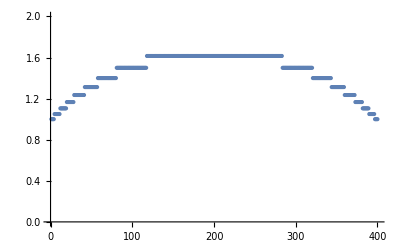

```mathematica
ListPlot[Table[PulsesPerPixelNormPract[pix],{pix,NpixPartial/2,-NpixPartial/2+1,-1}],PlotRange->{0,2}]
```